```mathematica
p[z_]:=ListLinePlot[Table[{x,y},{x,Range[1,50,1]},{y,Range[1,50,1]}][[z]],PlotStyle->Gray]
```

```mathematica
line[z_]:=ListLinePlot[Table[{x,z},{x,Range[1,50,0.01]}],PlotStyle->Gray]
```

```mathematica
line1[z_]:=ListLinePlot[Table[{x,z},{x,Range[0,51,0.01]}],PlotStyle->Blue]
```

```mathematica
p1[z_]:=ListLinePlot[Table[{z,y},{y,Range[0,51,1]}],PlotStyle->Blue]
```

```mathematica
p[z_]:=ListLinePlot[Table[{x,y},{x,Range[1,50,1]},{y,Range[1,50,1]}][[z]],PlotStyle->Gray]
```

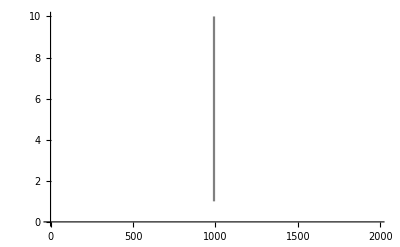

```mathematica
p[100]
```

```mathematica
line[z_]:=ListLinePlot[Table[{x,z},{x,Range[1,100,0.01]}],PlotStyle->Gray]
```

```mathematica
line1[z_]:=ListLinePlot[Table[{x,z},{x,Range[0,101,0.01]}],PlotStyle->Blue]
```

```mathematica
p1[z_]:=ListLinePlot[Table[{z,y},{y,Range[0,101,1]}],PlotStyle->Blue]
```

```mathematica
Clear[line,line1,p1]
```

```mathematica
LaunchKernels[4]
```

{KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…]}

```mathematica
lead= ParallelTable[ToExpression[Import["/home/shardulmukim/PhD/fwi/sq_lattice/50sq/leads/l"<>ToString[x]<>".dat"]],{x,Range[-2.5,2.5,0.01]}]
```

{1}
 |  |  |  |

```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->-t]
```

```mathematica
T[t_,m_]:=T[t,m]=t*IdentityMatrix[m]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_,m_]:=LEFT[ω,δ,t,ϵ,m]=Part[lead,Round[ω*100+251]]
```

```mathematica
g[ω_,δ_,t_,ϵ_,m_]:= Inverse[β[ω,δ,t,ϵ,m]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-g[ω,δ,t,ϵ,m].T[t,m].LEFT[ω,δ,t,ϵ,m].T[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-g[ω,δ,t,ϵ,m].T[t,m].LEFT[ω,δ,t,ϵ,m].T[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-SL[ω,δ,t,ϵ,m].T[t,m].SR[ω,δ,t,ϵ,m].T[t,m]].SL[ω,δ,t,ϵ,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-SR[ω,δ,t,ϵ,m].T[t,m].SL[ω,δ,t,ϵ,m].T[t,m]].SR[ω,δ,t,ϵ,m]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,m_]:= IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,m_]:= IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,m_]:= SR[ω,δ,t,ϵ,m].T[t,m].IL[ω,δ,t,ϵ,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,m_]:= Abs[Tr[gdd[ω,δ,t,ϵ,m].T[t,m].grr[ω,δ,t,ϵ,m].T[t,m]-T[t,m].GNON[ω,δ,t,ϵ,m].T[t,m].GNON[ω,δ,t,ϵ,m]]]
```

```mathematica
pris=ParallelTable[{ω,Abs[tr[ω,0.0001,1,0,50]]},{ω,Range[-2.5,2.5,0.01]}]//AbsoluteTiming
```

{5.57432,{{-2.5,21.},{-2.49,21.},{-2.48,21.},{-2.47,21.},{-2.46,21.},{-2.45,21.},{-2.44,21.},{-2.43,21.0005},{-2.42,22.},{-2.41,22.},{-2.4,22.},{-2.39,22.},{-2.38,22.},{-2.37,22.},{-2.36,22.},{-2.35,22.},{-2.34,22.},{-2.33,22.},{-2.32,22.},{-2.31,22.0002},{-2.3,22.9999},{-2.29,23.},{-2.28,23.},{-2.27,23.},{-2.26,23.},{-2.25,23.},{-2.24,23.},{-2.23,23.},{-2.22,23.},{-2.21,23.},{-2.2,23.},{-2.19,23.0001},{-2.18,23.9999},{-2.17,24.},{-2.16,24.},{-2.15,24.},{-2.14,24.},{-2.13,24.},{-2.12,24.},{-2.11,24.},{-2.1,24.},{-2.09,24.},{-2.08,24.},{-2.07,24.},{-2.06,24.999},{-2.05,25.},{-2.04,25.},{-2.03,25.},{-2.02,25.},{-2.01,25.},{-2.,25.},{-1.99,25.},{-1.98,25.},{-1.97,25.},{-1.96,25.},{-1.95,25.},{-1.94,25.001},{-1.93,26.},{-1.92,26.},{-1.91,26.},{-1.9,26.},{-1.89,26.},{-1.88,26.},{-1.87,26.},{-1.86,26.},{-1.85,26.},{-1.84,26.},{-1.83,26.},{-1.82,26.0001},{-1.81,26.9999},{-1.8,27.},{-1.79,27.},{-1.78,27.},{-1.77,27.},{-1.76,27.},{-1.75,27.},{-1.74,27.},{-1.73,27.},{-1.72,27.},{-1.71,27.},{-1.7,27.0001},{-1.69,27.9998},{-1.68,28.},{-1.67,28.},{-1.66,28.},{-1.65,28.},{-1.64,28.},{-1.63,28.},{-1.62,28.},{-1.61,28.},{-1.6,28.},{-1.59,28.},{-1.58,28.},{-1.57,28.9995},{-1.56,29.},{-1.55,29.},{-1.54,29.},{-1.53,29.},{-1.52,29.},{-1.51,29.},{-1.5,29.},{-1.49,29.},{-1.48,29.},{-1.47,29.},{-1.46,29.},{-1.45,29.9997},{-1.44,30.},{-1.43,30.},{-1.42,30.},{-1.41,30.},{-1.4,30.},{-1.39,30.},{-1.38,30.},{-1.37,30.},{-1.36,30.},{-1.35,30.},{-1.34,30.0001},{-1.33,30.9999},{-1.32,31.},{-1.31,31.},{-1.3,31.},{-1.29,31.},{-1.28,31.},{-1.27,31.},{-1.26,31.},{-1.25,31.},{-1.24,31.},{-1.23,31.},{-1.22,31.9869},{-1.21,32.},{-1.2,32.},{-1.19,32.},{-1.18,32.},{-1.17,32.},{-1.16,32.},{-1.15,32.},{-1.14,32.},{-1.13,32.},{-1.12,32.},{-1.11,32.0011},{-1.1,33.},{-1.09,33.},{-1.08,33.},{-1.07,33.},{-1.06,33.},{-1.05,33.},{-1.04,33.},{-1.03,33.},{-1.02,33.},{-1.01,33.},{-1.,33.5},{-0.99,34.},{-0.98,34.},{-0.97,34.},{-0.96,34.},{-0.95,34.},{-0.94,34.},{-0.93,34.},{-0.92,34.},{-0.91,34.},{-0.9,34.0001},{-0.89,34.9999},{-0.88,35.},{-0.87,35.},{-0.86,35.},{-0.85,35.},{-0.84,35.},{-0.83,35.},{-0.82,35.},{-0.81,35.},{-0.8,35.0001},{-0.79,35.9999},{-0.78,36.},{-0.77,36.},{-0.76,36.},{-0.75,36.},{-0.74,36.},{-0.73,36.},{-0.72,36.},{-0.71,36.},{-0.7,36.0016},{-0.69,37.},{-0.68,37.},{-0.67,37.},{-0.66,37.},{-0.65,37.},{-0.64,37.},{-0.63,37.},{-0.62,37.},{-0.61,37.0005},{-0.6,38.},{-0.59,38.},{-0.58,38.},{-0.57,38.},{-0.56,38.},{-0.55,38.},{-0.54,38.},{-0.53,38.},{-0.52,38.9994},{-0.51,39.},{-0.5,39.},{-0.49,39.},{-0.48,39.},{-0.47,39.},{-0.46,39.},{-0.45,39.},{-0.44,39.9993},{-0.43,40.},{-0.42,40.},{-0.41,40.},{-0.4,40.},{-0.39,40.},{-0.38,40.},{-0.37,40.0004},{-0.36,41.},{-0.35,41.},{-0.34,41.},{-0.33,41.},{-0.32,41.},{-0.31,41.},{-0.3,41.0127},{-0.29,42.},{-0.28,42.},{-0.27,42.},{-0.26,42.},{-0.25,42.},{-0.24,42.0006},{-0.23,43.},{-0.22,43.},{-0.21,43.},{-0.2,43.},{-0.19,43.0001},{-0.18,43.9997},{-0.17,44.},{-0.16,44.},{-0.15,44.},{-0.14,44.0001},{-0.13,44.9999},{-0.12,45.},{-0.11,45.},{-0.1,45.0001},{-0.09,45.9999},{-0.08,46.},{-0.07,46.},{-0.06,46.9855},{-0.05,47.},{-0.04,47.0001},{-0.03,47.9999},{-0.02,48.0001},{-0.01,48.9999},{0.,49.9996},{0.01,48.9999},{0.02,48.0001},{0.03,47.9999},{0.04,47.0001},{0.05,47.},{0.06,46.9855},{0.07,46.},{0.08,46.},{0.09,45.9999},{0.1,45.0001},{0.11,45.},{0.12,45.},{0.13,44.9999},{0.14,44.0001},{0.15,44.},{0.16,44.},{0.17,44.},{0.18,43.9997},{0.19,43.0001},{0.2,43.},{0.21,43.},{0.22,43.},{0.23,43.},{0.24,42.0006},{0.25,42.},{0.26,42.},{0.27,42.},{0.28,42.},{0.29,42.},{0.3,41.0127},{0.31,41.},{0.32,41.},{0.33,41.},{0.34,41.},{0.35,41.},{0.36,41.},{0.37,40.0004},{0.38,40.},{0.39,40.},{0.4,40.},{0.41,40.},{0.42,40.},{0.43,40.},{0.44,39.9993},{0.45,39.},{0.46,39.},{0.47,39.},{0.48,39.},{0.49,39.},{0.5,39.},{0.51,39.},{0.52,38.9994},{0.53,38.},{0.54,38.},{0.55,38.},{0.56,38.},{0.57,38.},{0.58,38.},{0.59,38.},{0.6,38.},{0.61,37.0005},{0.62,37.},{0.63,37.},{0.64,37.},{0.65,37.},{0.66,37.},{0.67,37.},{0.68,37.},{0.69,37.},{0.7,36.0016},{0.71,36.},{0.72,36.},{0.73,36.},{0.74,36.},{0.75,36.},{0.76,36.},{0.77,36.},{0.78,36.},{0.79,35.9999},{0.8,35.0001},{0.81,35.},{0.82,35.},{0.83,35.},{0.84,35.},{0.85,35.},{0.86,35.},{0.87,35.},{0.88,35.},{0.89,34.9999},{0.9,34.0001},{0.91,34.},{0.92,34.},{0.93,34.},{0.94,34.},{0.95,34.},{0.96,34.},{0.97,34.},{0.98,34.},{0.99,34.},{1.,33.5},{1.01,33.},{1.02,33.},{1.03,33.},{1.04,33.},{1.05,33.},{1.06,33.},{1.07,33.},{1.08,33.},{1.09,33.},{1.1,33.},{1.11,32.0011},{1.12,32.},{1.13,32.},{1.14,32.},{1.15,32.},{1.16,32.},{1.17,32.},{1.18,32.},{1.19,32.},{1.2,32.},{1.21,32.},{1.22,31.9869},{1.23,31.},{1.24,31.},{1.25,31.},{1.26,31.},{1.27,31.},{1.28,31.},{1.29,31.},{1.3,31.},{1.31,31.},{1.32,31.},{1.33,30.9999},{1.34,30.0001},{1.35,30.},{1.36,30.},{1.37,30.},{1.38,30.},{1.39,30.},{1.4,30.},{1.41,30.},{1.42,30.},{1.43,30.},{1.44,30.},{1.45,29.9997},{1.46,29.},{1.47,29.},{1.48,29.},{1.49,29.},{1.5,29.},{1.51,29.},{1.52,29.},{1.53,29.},{1.54,29.},{1.55,29.},{1.56,29.},{1.57,28.9995},{1.58,28.},{1.59,28.},{1.6,28.},{1.61,28.},{1.62,28.},{1.63,28.},{1.64,28.},{1.65,28.},{1.66,28.},{1.67,28.},{1.68,28.},{1.69,27.9998},{1.7,27.0001},{1.71,27.},{1.72,27.},{1.73,27.},{1.74,27.},{1.75,27.},{1.76,27.},{1.77,27.},{1.78,27.},{1.79,27.},{1.8,27.},{1.81,26.9999},{1.82,26.0001},{1.83,26.},{1.84,26.},{1.85,26.},{1.86,26.},{1.87,26.},{1.88,26.},{1.89,26.},{1.9,26.},{1.91,26.},{1.92,26.},{1.93,26.},{1.94,25.001},{1.95,25.},{1.96,25.},{1.97,25.},{1.98,25.},{1.99,25.},{2.,25.},{2.01,25.},{2.02,25.},{2.03,25.},{2.04,25.},{2.05,25.},{2.06,24.999},{2.07,24.},{2.08,24.},{2.09,24.},{2.1,24.},{2.11,24.},{2.12,24.},{2.13,24.},{2.14,24.},{2.15,24.},{2.16,24.},{2.17,24.},{2.18,23.9999},{2.19,23.0001},{2.2,23.},{2.21,23.},{2.22,23.},{2.23,23.},{2.24,23.},{2.25,23.},{2.26,23.},{2.27,23.},{2.28,23.},{2.29,23.},{2.3,22.9999},{2.31,22.0002},{2.32,22.},{2.33,22.},{2.34,22.},{2.35,22.},{2.36,22.},{2.37,22.},{2.38,22.},{2.39,22.},{2.4,22.},{2.41,22.},{2.42,22.},{2.43,21.0005},{2.44,21.},{2.45,21.},{2.46,21.},{2.47,21.},{2.48,21.},{2.49,21.},{2.5,21.}}}

```mathematica
tr1=Compile[{ω},tr[ω,0.0001,1,0,50],CompilationTarget->"C",CompilationOptions->{"ExpressionOptimization" -> True},Parallelization->True]
```

CompiledFunction[…]

```mathematica
pris=ParallelTable[{ω,tr1[ω]},{ω,Range[-2.5,2.5,0.01]}]
```

{{-2.5,21.},{-2.49,21.},{-2.48,21.},{-2.47,21.},{-2.46,21.},{-2.45,21.},{-2.44,21.},{-2.43,21.0005},{-2.42,22.},{-2.41,22.},{-2.4,22.},{-2.39,22.},{-2.38,22.},{-2.37,22.},{-2.36,22.},{-2.35,22.},{-2.34,22.},{-2.33,22.},{-2.32,22.},{-2.31,22.0002},{-2.3,22.9999},{-2.29,23.},{-2.28,23.},{-2.27,23.},{-2.26,23.},{-2.25,23.},{-2.24,23.},{-2.23,23.},{-2.22,23.},{-2.21,23.},{-2.2,23.},{-2.19,23.0001},{-2.18,23.9999},{-2.17,24.},{-2.16,24.},{-2.15,24.},{-2.14,24.},{-2.13,24.},{-2.12,24.},{-2.11,24.},{-2.1,24.},{-2.09,24.},{-2.08,24.},{-2.07,24.},{-2.06,24.999},{-2.05,25.},{-2.04,25.},{-2.03,25.},{-2.02,25.},{-2.01,25.},{-2.,25.},{-1.99,25.},{-1.98,25.},{-1.97,25.},{-1.96,25.},{-1.95,25.},{-1.94,25.001},{-1.93,26.},{-1.92,26.},{-1.91,26.},{-1.9,26.},{-1.89,26.},{-1.88,26.},{-1.87,26.},{-1.86,26.},{-1.85,26.},{-1.84,26.},{-1.83,26.},{-1.82,26.0001},{-1.81,26.9999},{-1.8,27.},{-1.79,27.},{-1.78,27.},{-1.77,27.},{-1.76,27.},{-1.75,27.},{-1.74,27.},{-1.73,27.},{-1.72,27.},{-1.71,27.},{-1.7,27.0001},{-1.69,27.9998},{-1.68,28.},{-1.67,28.},{-1.66,28.},{-1.65,28.},{-1.64,28.},{-1.63,28.},{-1.62,28.},{-1.61,28.},{-1.6,28.},{-1.59,28.},{-1.58,28.},{-1.57,28.9995},{-1.56,29.},{-1.55,29.},{-1.54,29.},{-1.53,29.},{-1.52,29.},{-1.51,29.},{-1.5,29.},{-1.49,29.},{-1.48,29.},{-1.47,29.},{-1.46,29.},{-1.45,29.9997},{-1.44,30.},{-1.43,30.},{-1.42,30.},{-1.41,30.},{-1.4,30.},{-1.39,30.},{-1.38,30.},{-1.37,30.},{-1.36,30.},{-1.35,30.},{-1.34,30.0001},{-1.33,30.9999},{-1.32,31.},{-1.31,31.},{-1.3,31.},{-1.29,31.},{-1.28,31.},{-1.27,31.},{-1.26,31.},{-1.25,31.},{-1.24,31.},{-1.23,31.},{-1.22,31.9869},{-1.21,32.},{-1.2,32.},{-1.19,32.},{-1.18,32.},{-1.17,32.},{-1.16,32.},{-1.15,32.},{-1.14,32.},{-1.13,32.},{-1.12,32.},{-1.11,32.0011},{-1.1,33.},{-1.09,33.},{-1.08,33.},{-1.07,33.},{-1.06,33.},{-1.05,33.},{-1.04,33.},{-1.03,33.},{-1.02,33.},{-1.01,33.},{-1.,33.5},{-0.99,34.},{-0.98,34.},{-0.97,34.},{-0.96,34.},{-0.95,34.},{-0.94,34.},{-0.93,34.},{-0.92,34.},{-0.91,34.},{-0.9,34.0001},{-0.89,34.9999},{-0.88,35.},{-0.87,35.},{-0.86,35.},{-0.85,35.},{-0.84,35.},{-0.83,35.},{-0.82,35.},{-0.81,35.},{-0.8,35.0001},{-0.79,35.9999},{-0.78,36.},{-0.77,36.},{-0.76,36.},{-0.75,36.},{-0.74,36.},{-0.73,36.},{-0.72,36.},{-0.71,36.},{-0.7,36.0016},{-0.69,37.},{-0.68,37.},{-0.67,37.},{-0.66,37.},{-0.65,37.},{-0.64,37.},{-0.63,37.},{-0.62,37.},{-0.61,37.0005},{-0.6,38.},{-0.59,38.},{-0.58,38.},{-0.57,38.},{-0.56,38.},{-0.55,38.},{-0.54,38.},{-0.53,38.},{-0.52,38.9994},{-0.51,39.},{-0.5,39.},{-0.49,39.},{-0.48,39.},{-0.47,39.},{-0.46,39.},{-0.45,39.},{-0.44,39.9993},{-0.43,40.},{-0.42,40.},{-0.41,40.},{-0.4,40.},{-0.39,40.},{-0.38,40.},{-0.37,40.0004},{-0.36,41.},{-0.35,41.},{-0.34,41.},{-0.33,41.},{-0.32,41.},{-0.31,41.},{-0.3,41.0127},{-0.29,42.},{-0.28,42.},{-0.27,42.},{-0.26,42.},{-0.25,42.},{-0.24,42.0006},{-0.23,43.},{-0.22,43.},{-0.21,43.},{-0.2,43.},{-0.19,43.0001},{-0.18,43.9997},{-0.17,44.},{-0.16,44.},{-0.15,44.},{-0.14,44.0001},{-0.13,44.9999},{-0.12,45.},{-0.11,45.},{-0.1,45.0001},{-0.09,45.9999},{-0.08,46.},{-0.07,46.},{-0.06,46.9855},{-0.05,47.},{-0.04,47.0001},{-0.03,47.9999},{-0.02,48.0001},{-0.01,48.9999},{0.,49.9996},{0.01,48.9999},{0.02,48.0001},{0.03,47.9999},{0.04,47.0001},{0.05,47.},{0.06,46.9855},{0.07,46.},{0.08,46.},{0.09,45.9999},{0.1,45.0001},{0.11,45.},{0.12,45.},{0.13,44.9999},{0.14,44.0001},{0.15,44.},{0.16,44.},{0.17,44.},{0.18,43.9997},{0.19,43.0001},{0.2,43.},{0.21,43.},{0.22,43.},{0.23,43.},{0.24,42.0006},{0.25,42.},{0.26,42.},{0.27,42.},{0.28,42.},{0.29,42.},{0.3,41.0127},{0.31,41.},{0.32,41.},{0.33,41.},{0.34,41.},{0.35,41.},{0.36,41.},{0.37,40.0004},{0.38,40.},{0.39,40.},{0.4,40.},{0.41,40.},{0.42,40.},{0.43,40.},{0.44,39.9993},{0.45,39.},{0.46,39.},{0.47,39.},{0.48,39.},{0.49,39.},{0.5,39.},{0.51,39.},{0.52,38.9994},{0.53,38.},{0.54,38.},{0.55,38.},{0.56,38.},{0.57,38.},{0.58,38.},{0.59,38.},{0.6,38.},{0.61,37.0005},{0.62,37.},{0.63,37.},{0.64,37.},{0.65,37.},{0.66,37.},{0.67,37.},{0.68,37.},{0.69,37.},{0.7,36.0016},{0.71,36.},{0.72,36.},{0.73,36.},{0.74,36.},{0.75,36.},{0.76,36.},{0.77,36.},{0.78,36.},{0.79,35.9999},{0.8,35.0001},{0.81,35.},{0.82,35.},{0.83,35.},{0.84,35.},{0.85,35.},{0.86,35.},{0.87,35.},{0.88,35.},{0.89,34.9999},{0.9,34.0001},{0.91,34.},{0.92,34.},{0.93,34.},{0.94,34.},{0.95,34.},{0.96,34.},{0.97,34.},{0.98,34.},{0.99,34.},{1.,33.5},{1.01,33.},{1.02,33.},{1.03,33.},{1.04,33.},{1.05,33.},{1.06,33.},{1.07,33.},{1.08,33.},{1.09,33.},{1.1,33.},{1.11,32.0011},{1.12,32.},{1.13,32.},{1.14,32.},{1.15,32.},{1.16,32.},{1.17,32.},{1.18,32.},{1.19,32.},{1.2,32.},{1.21,32.},{1.22,31.9869},{1.23,31.},{1.24,31.},{1.25,31.},{1.26,31.},{1.27,31.},{1.28,31.},{1.29,31.},{1.3,31.},{1.31,31.},{1.32,31.},{1.33,30.9999},{1.34,30.0001},{1.35,30.},{1.36,30.},{1.37,30.},{1.38,30.},{1.39,30.},{1.4,30.},{1.41,30.},{1.42,30.},{1.43,30.},{1.44,30.},{1.45,29.9997},{1.46,29.},{1.47,29.},{1.48,29.},{1.49,29.},{1.5,29.},{1.51,29.},{1.52,29.},{1.53,29.},{1.54,29.},{1.55,29.},{1.56,29.},{1.57,28.9995},{1.58,28.},{1.59,28.},{1.6,28.},{1.61,28.},{1.62,28.},{1.63,28.},{1.64,28.},{1.65,28.},{1.66,28.},{1.67,28.},{1.68,28.},{1.69,27.9998},{1.7,27.0001},{1.71,27.},{1.72,27.},{1.73,27.},{1.74,27.},{1.75,27.},{1.76,27.},{1.77,27.},{1.78,27.},{1.79,27.},{1.8,27.},{1.81,26.9999},{1.82,26.0001},{1.83,26.},{1.84,26.},{1.85,26.},{1.86,26.},{1.87,26.},{1.88,26.},{1.89,26.},{1.9,26.},{1.91,26.},{1.92,26.},{1.93,26.},{1.94,25.001},{1.95,25.},{1.96,25.},{1.97,25.},{1.98,25.},{1.99,25.},{2.,25.},{2.01,25.},{2.02,25.},{2.03,25.},{2.04,25.},{2.05,25.},{2.06,24.999},{2.07,24.},{2.08,24.},{2.09,24.},{2.1,24.},{2.11,24.},{2.12,24.},{2.13,24.},{2.14,24.},{2.15,24.},{2.16,24.},{2.17,24.},{2.18,23.9999},{2.19,23.0001},{2.2,23.},{2.21,23.},{2.22,23.},{2.23,23.},{2.24,23.},{2.25,23.},{2.26,23.},{2.27,23.},{2.28,23.},{2.29,23.},{2.3,22.9999},{2.31,22.0002},{2.32,22.},{2.33,22.},{2.34,22.},{2.35,22.},{2.36,22.},{2.37,22.},{2.38,22.},{2.39,22.},{2.4,22.},{2.41,22.},{2.42,22.},{2.43,21.0005},{2.44,21.},{2.45,21.},{2.46,21.},{2.47,21.},{2.48,21.},{2.49,21.},{2.5,21.}}

```mathematica
list1={{imp21,imp46,imp31,imp4,imp48,imp25,imp33,imp5,imp24,imp50,imp9,imp43,imp47,imp34,imp40,imp27,imp6,imp12,imp41,imp10,imp32,imp20,imp42,imp18,imp14,imp45,imp36,imp13,imp44,imp28,imp17,imp49,imp3,imp38,imp1,imp35,imp16,imp29,imp7,imp19,imp8,imp15,imp23,imp22,imp11,imp37,imp2,imp30,imp39,imp26}}
```

{{imp21,imp46,imp31,imp4,imp48,imp25,imp33,imp5,imp24,imp50,imp9,imp43,imp47,imp34,imp40,imp27,imp6,imp12,imp41,imp10,imp32,imp20,imp42,imp18,imp14,imp45,imp36,imp13,imp44,imp28,imp17,imp49,imp3,imp38,imp1,imp35,imp16,imp29,imp7,imp19,imp8,imp15,imp23,imp22,imp11,imp37,imp2,imp30,imp39,imp26}}

```mathematica
Clear[imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14,imp15,imp16,imp17,imp18,imp19,imp20,imp21,imp22,imp23,imp24,imp25,imp26,imp27,imp28,imp29,imp30,imp31,imp32,imp33,imp34,imp35,imp36,imp37,imp38,imp39,imp40,imp41,imp42,imp43,imp44,imp45,imp46,imp47,imp48,imp49,imp50]
aa=RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14,imp15,imp16,imp17,imp18,imp19,imp20,imp21,imp22,imp23,imp24,imp25,imp26,imp27,imp28,imp29,imp30,imp31,imp32,imp33,imp34,imp35,imp36,imp37,imp38,imp39,imp40,imp41,imp42,imp43,imp44,imp45,imp46,imp47,imp48,imp49,imp50}]
bb:=Flatten[Table[Position[Flatten[Table[Position[aa,ToExpression[Table["imp"<>ToString[x]<>"",{x,50}][[y]]]],{y,50}]],z],{z,50}]]
cc:=Flatten[Table[Position[bb,x],{x,Range[1,50,1]}]]
dd=ToExpression[Table["imp"<>ToString[z]<>"",{z,cc}]]
leftright= Transpose[Join[{Range[1,50,1]},{bb}]]
downup= Transpose[Join[{cc},{Range[1,50,1]}]]
```

{imp40,imp35,imp22,imp49,imp9,imp29,imp28,imp42,imp34,imp2,imp17,imp38,imp21,imp20,imp47,imp15,imp4,imp37,imp16,imp27,imp10,imp19,imp32,imp45,imp41,imp13,imp39,imp12,imp30,imp14,imp48,imp11,imp46,imp43,imp7,imp6,imp36,imp31,imp33,imp8,imp50,imp18,imp44,imp5,imp25,imp26,imp1,imp23,imp3,imp24}

{imp47,imp10,imp49,imp17,imp44,imp36,imp35,imp40,imp5,imp21,imp32,imp28,imp26,imp30,imp16,imp19,imp11,imp42,imp22,imp14,imp13,imp3,imp48,imp50,imp45,imp46,imp20,imp7,imp6,imp29,imp38,imp23,imp39,imp9,imp2,imp37,imp18,imp12,imp27,imp1,imp25,imp8,imp34,imp43,imp24,imp33,imp15,imp31,imp4,imp41}

{{1,40},{2,35},{3,22},{4,49},{5,9},{6,29},{7,28},{8,42},{9,34},{10,2},{11,17},{12,38},{13,21},{14,20},{15,47},{16,15},{17,4},{18,37},{19,16},{20,27},{21,10},{22,19},{23,32},{24,45},{25,41},{26,13},{27,39},{28,12},{29,30},{30,14},{31,48},{32,11},{33,46},{34,43},{35,7},{36,6},{37,36},{38,31},{39,33},{40,8},{41,50},{42,18},{43,44},{44,5},{45,25},{46,26},{47,1},{48,23},{49,3},{50,24}}

{{47,1},{10,2},{49,3},{17,4},{44,5},{36,6},{35,7},{40,8},{5,9},{21,10},{32,11},{28,12},{26,13},{30,14},{16,15},{19,16},{11,17},{42,18},{22,19},{14,20},{13,21},{3,22},{48,23},{50,24},{45,25},{46,26},{20,27},{7,28},{6,29},{29,30},{38,31},{23,32},{39,33},{9,34},{2,35},{37,36},{18,37},{12,38},{27,39},{1,40},{25,41},{8,42},{34,43},{43,44},{24,45},{33,46},{15,47},{31,48},{4,49},{41,50}}

```mathematica
(*imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{1,1}}->ω+ⅈ*0.0001-ϵ1]]];imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{2,2}}->ω+ⅈ*0.0001-ϵ1]]];imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{3,3}}->ω+ⅈ*0.0001-ϵ1]]];imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{4,4}}->ω+ⅈ*0.0001-ϵ1]]];imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{5,5}}->ω+ⅈ*0.0001-ϵ1]]];imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{6,6}}->ω+ⅈ*0.0001-ϵ1]]];imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{7,7}}->ω+ⅈ*0.0001-ϵ1]]];imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{8,8}}->ω+ⅈ*0.0001-ϵ1]]];imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{9,9}}->ω+ⅈ*0.0001-ϵ1]]];imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-ϵ1]]];imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{11,11}}->ω+ⅈ*0.0001-ϵ1]]];imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{12,12}}->ω+ⅈ*0.0001-ϵ1]]];imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{13,13}}->ω+ⅈ*0.0001-ϵ1]]];imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-ϵ1]]];imp15:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{15,15}}->ω+ⅈ*0.0001-ϵ1]]];imp16:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{16,16}}->ω+ⅈ*0.0001-ϵ1]]];imp17:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{17,17}}->ω+ⅈ*0.0001-ϵ1]]];imp18:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{18,18}}->ω+ⅈ*0.0001-ϵ1]]];imp19:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{19,19}}->ω+ⅈ*0.0001-ϵ1]]];imp20:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{20,20}}->ω+ⅈ*0.0001-ϵ1]]];imp21:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{21,21}}->ω+ⅈ*0.0001-ϵ1]]];imp22:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{22,22}}->ω+ⅈ*0.0001-ϵ1]]];imp23:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{23,23}}->ω+ⅈ*0.0001-ϵ1]]];imp24:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{24,24}}->ω+ⅈ*0.0001-ϵ1]]];imp25:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{25,25}}->ω+ⅈ*0.0001-ϵ1]]];imp26:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{26,26}}->ω+ⅈ*0.0001-ϵ1]]];imp27:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{27,27}}->ω+ⅈ*0.0001-ϵ1]]];imp28:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{28,28}}->ω+ⅈ*0.0001-ϵ1]]];imp29:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{29,29}}->ω+ⅈ*0.0001-ϵ1]]];imp30:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{30,30}}->ω+ⅈ*0.0001-ϵ1]]];imp31:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{31,31}}->ω+ⅈ*0.0001-ϵ1]]];imp32:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{32,32}}->ω+ⅈ*0.0001-ϵ1]]];imp33:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{33,33}}->ω+ⅈ*0.0001-ϵ1]]];imp34:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{34,34}}->ω+ⅈ*0.0001-ϵ1]]];imp35:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{35,35}}->ω+ⅈ*0.0001-ϵ1]]];imp36:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{36,36}}->ω+ⅈ*0.0001-ϵ1]]];imp37:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{37,37}}->ω+ⅈ*0.0001-ϵ1]]];imp38:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{38,38}}->ω+ⅈ*0.0001-ϵ1]]];imp39:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{39,39}}->ω+ⅈ*0.0001-ϵ1]]];imp40:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{40,40}}->ω+ⅈ*0.0001-ϵ1]]];imp41:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{41,41}}->ω+ⅈ*0.0001-ϵ1]]];imp42:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{42,42}}->ω+ⅈ*0.0001-ϵ1]]];imp43:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{43,43}}->ω+ⅈ*0.0001-ϵ1]]];imp44:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{44,44}}->ω+ⅈ*0.0001-ϵ1]]];imp45:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{45,45}}->ω+ⅈ*0.0001-ϵ1]]];imp46:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{46,46}}->ω+ⅈ*0.0001-ϵ1]]];imp47:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{47,47}}->ω+ⅈ*0.0001-ϵ1]]];imp48:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{48,48}}->ω+ⅈ*0.0001-ϵ1]]];imp49:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{49,49}}->ω+ⅈ*0.0001-ϵ1]]];imp50:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{50,50}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-0]]];*)
```

```mathematica
im[ω_,μ_,λ_,q_,ϵ1_,m_]:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ,μ},{λ,λ},{q,q}}->ω+ⅈ*0.0001-ϵ1]]]
```

```mathematica
im4[ω_,μ_,λ_,q_,r_,ϵ1_,m_]:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ,μ},{λ,λ},{q,q},{r,r}}->ω+ⅈ*0.0001-ϵ1]]]
```

```mathematica
im5[ω_,μ_,λ_,q_,r_,s_,ϵ1_,m_]:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ,μ},{λ,λ},{q,q},{r,r},{s,s}}->ω+ⅈ*0.0001-ϵ1]]]
```

```mathematica
im6[ω_,μ_,λ_,q_,r_,s_,z_,ϵ1_,m_]:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ,μ},{λ,λ},{q,q},{r,r},{s,s},{z,z}}->ω+ⅈ*0.0001-ϵ1]]]
```

```mathematica
testhori[1,0.5,0,50,0,0,1,5,0,0,0]
```

32.3821

```mathematica
testhori[ω_,ϵ1_,ϵ_,m_,y_,x_,a_,b_,μ_,λ_,q_]:=Module[{Tin=T[1,m],T1=T[1,m],list1,list2,tra},
tra:=Module[{J=LEFT[ω,0.0001,1,0,m]},
list1={{im[ω,44,45,45,ϵ1,m],im[ω,26,32,32,ϵ1,m],im[ω,48,48,50,ϵ1,m],im[ω,μ,λ,q,0,m],im[ω,9,9,9,ϵ1,m],im[ω,41,41,41,ϵ1,m],im[ω,48,48,48,ϵ1,m],im[ω,16,50,24,ϵ1,m],im[ω,7,48,25,ϵ1,m],im[ω,13,14,30,ϵ1,m],im[ω,25,35,45,ϵ1,m],im[ω,μ,λ,q,0,m],im[ω,μ,λ,26,ϵ1,m],im[ω,10,21,39,ϵ1,m],im[ω,5,5,49,ϵ1,m],im[ω,μ,λ,q,0,m],im5[ω,10,28,31,46,47,ϵ1,m],im[ω,45,λ,q,ϵ1,m],im[ω,μ,λ,q,0,m],im[ω,23,λ,q,ϵ1,m],im[ω,μ,λ,q,0,m],im[ω,15,36,q,ϵ1,m],im[ω,47,λ,q,ϵ1,m],im5[ω,18,21,35,43,46,ϵ1,m],im[ω,6,λ,q,ϵ1,m],im5[ω,8,23,28,40,44,ϵ1,m],im[ω,13,24,q,ϵ1,m],im[ω,9,40,q,ϵ1,m],im[ω,35,0,0,ϵ1,m],im[ω,34,0,0,ϵ1,m],im4[ω,1,34,45,46,ϵ1,m],im[ω,10,47,0,ϵ1,m],im[ω,1,0,0,ϵ1,m],im4[ω,12,24,38,48,ϵ1,m],im[ω,19,21,q,ϵ1,m],im[ω,50,λ,q,ϵ1,m],im4[ω,39,45,19,5,ϵ1,m],im4[ω,8,22,23,31,ϵ1,m],im[ω,37,45,0,ϵ1,m],im5[ω,9,6,30,37,50,ϵ1,m],im[ω,μ,4,49,ϵ1,m],im[ω,μ,λ,q,0,m],im[ω,μ,λ,27,ϵ1,m],im[ω,μ,λ,34,ϵ1,m],im[ω,μ,39,29,ϵ1,m],im[ω,μ,λ,q,0,m],im[ω,μ,25,8,ϵ1,m],im[ω,μ,λ,q,0,m],im[ω,9,10,33,ϵ1,m],im4[ω,41,45,27,8,ϵ1,m]}};
b1=Module[{},
sl1= Module[{},Do[J=Inverse[IdentityMatrix[m]-list1[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list1[[1,ζ]],{ζ,a,b}];
 J=J];
Il1:=Inverse[IdentityMatrix[m]-sl1.T1.J.T1].sl1;
Ir1:=Inverse[IdentityMatrix[m]-J.T1.sl1.T1].J;gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= J.T1.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]]];
b1];
tra]
```

```mathematica
Clear[h,m1]
```

```mathematica
h=Compile[{ω,a,b},testhori[ω,0.5,0,50,-2.5,2.5,a,b,0,0,0],CompilationTarget->"C",CompilationOptions->{"ExpressionOptimization" -> True},Parallelization->True]
```

CompiledFunction[…]

```mathematica
h[1,1,5]
```

32.3821

```mathematica
v=Compile[{ω,a,b},testhori[ω,0.5,0,50,-2.5,2.5,a,b,0,0,0],CompilationTarget->"C",CompilationOptions->{"ExpressionOptimization" -> True},Parallelization->True]
```

CompiledFunction[…]

```mathematica
m1[a_,b_]:=m1[a,b]=ParallelTable[{ω,h[ω,a,b]},{ω,Range[-2.5,2.5,0.01]}]
```

```mathematica
m2[a_,b_]:=ParallelTable[{ω,v[ω,a,b]},{ω,Range[-2.5,2.5,0.01]}]
```

```mathematica
hori[a_,b_,y_,x_]:=Module[{},ρ1:=Module[{B1=Transpose[{m1[a,b][[1;;501]][[;;,1]],(m1[a,b][[1;;501,2]]-pris[[2]][[1;;501,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];
ρ2:=Module[{B1=Transpose[{m1[a,b][[1;;501]][[;;,1]],(m1[a,b][[1;;501,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/50sq/1per.dat"][[1;;501,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m1[a,b][[1;;501]][[;;,1]],(m1[a,b][[1;;501,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/50sq/2per.dat"][[1;;501,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m1[a,b][[1;;501]][[;;,1]],(m1[a,b][[1;;501,2]]-Import["/home/shardulmukim/PhD/fwi/sq_lattice/50sq/3per.dat"][[1;;501,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m1[a,b][[1;;501]][[;;,1]],(m1[a,b][[1;;501,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/50sq/4per.dat"][[1;;501,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m1[a,b][[1;;501]][[;;,1]],(m1[a,b][[1;;501,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/50sq/5per.dat"][[1;;501,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m1[a,b][[1;;501]][[;;,1]],(m1[a,b][[1;;501,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/50sq/6per.dat"][[1;;501,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ8:=Module[{B1=Transpose[{m1[a,b][[1;;501]][[;;,1]],(m1[a,b][[1;;501,2]]-Import["/home/shardulmukim/PhD/fwi/sq_lattice/50sq/7per.dat"][[1;;501,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7,ρ8}]
```

```mathematica
vert[a_,b_,y_,x_]:=Module[{},ρ1:=Module[{B1=Transpose[{m2[a,b][[1;;501]][[;;,1]],(m2[a,b][[1;;501,2]]-pris[[2]][[1;;501,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];
ρ2:=Module[{B1=Transpose[{m2[a,b][[1;;501]][[;;,1]],(m2[a,b][[1;;501,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/50sq/1per.dat"][[1;;501,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m2[a,b][[1;;501]][[;;,1]],(m2[a,b][[1;;501,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/50sq/2per.dat"][[1;;501,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m2[a,b][[1;;501]][[;;,1]],(m2[a,b][[1;;501,2]]-Import["/home/shardulmukim/PhD/fwi/sq_lattice/50sq/3per.dat"][[1;;501,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m2[a,b][[1;;501]][[;;,1]],(m2[a,b][[1;;501,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/50sq/4per.dat"][[1;;501,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m2[a,b][[1;;501]][[;;,1]],(m2[a,b][[1;;501,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/50sq/5per.dat"][[1;;501,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m2[a,b][[1;;501]][[;;,1]],(m2[a,b][[1;;501,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/50sq/6per.dat"][[1;;501,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ8:=Module[{B1=Transpose[{m2[a,b][[1;;501]][[;;,1]],(m2[a,b][[1;;501,2]]-Import["/home/shardulmukim//PhD/fwi/sq_lattice/50sq/7per.dat"][[1;;501,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7}]
```

CompiledFunction[…]

CompiledFunction[…]

```mathematica
Join[{hori[1,5,0,2.5]},{hori[6,10,0,2.5]},{hori[11,15,0,2.5]},{hori[16,20,0,2.5]},{hori[21,25,0,2.5]},{hori[26,30,0,2.5]},{hori[31,35,0,2.5]},{hori[36,40,0,2.5]},{hori[41,45,0,2.5]},{hori[46,50,0,2.5]}]
```

{{0.0332694,0.112322,0.197087,0.342888,0.42943,0.532566,0.617869},{0.0347972,0.0972941,0.170359,0.301022,0.380438,0.475609,0.554869},{0.0316942,0.103272,0.182455,0.321111,0.405984,0.509222,0.594349},{0.0319877,0.106978,0.188609,0.330351,0.415684,0.518661,0.604045},{0.0324147,0.100988,0.178329,0.314849,0.397704,0.497351,0.580265},{0.0340228,0.0950564,0.166987,0.295535,0.3742,0.469383,0.549189},{0.0366614,0.0935358,0.163191,0.289509,0.367011,0.459947,0.537628},{0.0372061,0.0933877,0.163009,0.289587,0.367725,0.461733,0.539942},{0.0325327,0.114852,0.201323,0.350535,0.440293,0.548495,0.636777},{0.0316835,0.105427,0.186005,0.32676,0.412415,0.515664,0.600624}}

```mathematica
Flatten[Table[Position[%108[[x]],Min[%108[[x]]]],{x,10}]]
```

{1,1,1,1,1,1,1,1,1,1}

```mathematica
hori[41,45,-2.5,2.5]
```

{0.0199979,0.0709716,0.120596,0.204416,0.255715,0.318545,0.368797}

```mathematica
Table[hori[a,a+4,-2.5,2.5],{a,Range[1,50,5]}]
```

$Aborted

```mathematica
aver=Table[vert[a,a+4,-2.5,2.5],{a,Range[1,50,5]}]
ahor=Table[hori[a,a+4,-2.5,2.5],{a,Range[1,50,5]}]
Flatten[Table[Position[ahor[[x]],Min[ahor[[x]]]],{x,10}]]
Flatten[Table[Position[aver[[x]],Min[aver[[x]]]],{x,10}]]
```

CompiledFunction::cfse: Compiled expression testhori[-2.5,0.5,0,50,-2.5,2.5,2,1.,5.,0,0,0] should be a machine-size real number.

CompiledFunction::cfse: Compiled expression testhori[-2.24,0.5,0,50,-2.5,2.5,2,1.,5.,0,0,0] should be a machine-size real number.

CompiledFunction::cfse: Compiled expression testhori[-1.99,0.5,0,50,-2.5,2.5,2,1.,5.,0,0,0] should be a machine-size real number.

CompiledFunction::cfse: Compiled expression testhori[-1.74,0.5,0,50,-2.5,2.5,2,1.,5.,0,0,0] should be a machine-size real number.

CompiledFunction::cfexe: Could not complete external evaluation; proceeding with uncompiled evaluation.

CompiledFunction::cfse: Compiled expression testhori[-2.49,0.5,0,50,-2.5,2.5,2,1.,5.,0,0,0] should be a machine-size real number.

CompiledFunction::cfse: Compiled expression testhori[-2.23,0.5,0,50,-2.5,2.5,2,1.,5.,0,0,0] should be a machine-size real number.

CompiledFunction::cfse: Compiled expression testhori[-1.98,0.5,0,50,-2.5,2.5,2,1.,5.,0,0,0] should be a machine-size real number.

CompiledFunction::cfse: Compiled expression testhori[-1.73,0.5,0,50,-2.5,2.5,2,1.,5.,0,0,0] should be a machine-size real number.

CompiledFunction::cfexe: Could not complete external evaluation; proceeding with uncompiled evaluation.

CompiledFunction::cfse: Compiled expression testhori[-2.48,0.5,0,50,-2.5,2.5,2,1.,5.,0,0,0] should be a machine-size real number.

CompiledFunction::cfse: Compiled expression testhori[-2.22,0.5,0,50,-2.5,2.5,2,1.,5.,0,0,0] should be a machine-size real number.

CompiledFunction::cfse: Compiled expression testhori[-1.97,0.5,0,50,-2.5,2.5,2,1.,5.,0,0,0] should be a machine-size real number.

CompiledFunction::cfse: Compiled expression testhori[-1.72,0.5,0,50,-2.5,2.5,2,1.,5.,0,0,0] should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfse will be suppressed during this calculation.

CompiledFunction::cfexe: Could not complete external evaluation; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfexe will be suppressed during this calculation.

$Aborted

CompiledFunction::cfse: Compiled expression testhori[-2.5,0.5,0,50,-2.5,2.5,1,1.,5.,0,0,0] should be a machine-size real number.

CompiledFunction::cfse: Compiled expression testhori[-2.24,0.5,0,50,-2.5,2.5,1,1.,5.,0,0,0] should be a machine-size real number.

CompiledFunction::cfse: Compiled expression testhori[-1.99,0.5,0,50,-2.5,2.5,1,1.,5.,0,0,0] should be a machine-size real number.

CompiledFunction::cfse: Compiled expression testhori[-1.74,0.5,0,50,-2.5,2.5,1,1.,5.,0,0,0] should be a machine-size real number.

CompiledFunction::cfexe: Could not complete external evaluation; proceeding with uncompiled evaluation.

CompiledFunction::cfse: Compiled expression testhori[-2.49,0.5,0,50,-2.5,2.5,1,1.,5.,0,0,0] should be a machine-size real number.

$Aborted

$Aborted[]

Part::partd: Part specification ahor⟦1⟧ is longer than depth of object.

Part::partd: Part specification ahor⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{}

Part::partd: Part specification aver⟦1⟧ is longer than depth of object.

Part::partd: Part specification aver⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{}

```mathematica
{{1,44},{1,45},{2,26},{2,32},{3,48},{3,50},{5,9},{6,41},{7,48},{8,16},{8,24},{8,50},{9,7},{9,25},{9,48},{10,13},{10,14},{10,30},{11,25},{11,35},{11,45},{13,26},{14,10},{14,21},{14,39},{15,5},{15,49},{17,10},{17,28},{17,31},{17,46},{17,47},{18,45},{20,23},{22,15},{22,36},{23,47},{24,18},{24,21},{24,35},{24,43},{24,46},{25,6},{26,8},{26,23},{26,28},{26,28},{26,40},{26,44},{27,13},{27,24},{28,9},{28,40},{29,35},{30,34},{31,1},{31,34},{31,45},{31,46},{32,10},{32,47},{33,1},{34,12},{34,24},{34,38},{34,48},{35,19},{35,19},{35,21},{36,50},{37,5},{37,19},{37,39},{37,45},{38,8},{38,22},{38,23},{38,31},{39,37},{39,45},{40,6},{40,9},{40,30},{40,37},{40,50},{41,4},{41,49},{43,27},{44,34},{45,29},{45,39},{47,8},{47,25},{49,9},{49,10},{49,33},{50,8},{50,27},{50,41},{50,45}}
```

{{1,44},{1,45},{2,26},{2,32},{3,48},{3,50},{5,9},{6,41},{7,48},{8,16},{8,24},{8,50},{9,7},{9,25},{9,48},{10,13},{10,14},{10,30},{11,25},{11,35},{11,45},{13,26},{14,10},{14,21},{14,39},{15,5},{15,49},{17,10},{17,28},{17,31},{17,46},{17,47},{18,45},{20,23},{22,15},{22,36},{23,47},{24,18},{24,21},{24,35},{24,43},{24,46},{25,6},{26,8},{26,23},{26,28},{26,28},{26,40},{26,44},{27,13},{27,24},{28,9},{28,40},{29,35},{30,34},{31,1},{31,34},{31,45},{31,46},{32,10},{32,47},{33,1},{34,12},{34,24},{34,38},{34,48},{35,19},{35,19},{35,21},{36,50},{37,5},{37,19},{37,39},{37,45},{38,8},{38,22},{38,23},{38,31},{39,37},{39,45},{40,6},{40,9},{40,30},{40,37},{40,50},{41,4},{41,49},{43,27},{44,34},{45,29},{45,39},{47,8},{47,25},{49,9},{49,10},{49,33},{50,8},{50,27},{50,41},{50,45}}

```mathematica
Show[Show[Show[Table[p[z],{z,50}],Table[line[z],{z,50}],PlotRange->All],Show[line1[0.5],line1[5.5],line1[10.5],line1[15.5],line1[20.5],line1[25.5],line1[30.5],line1[35.5],line1[40.5],line1[45.5],line1[50.5],PlotRange->All],Show[p1[0.5],p1[5.5],p1[10.5],p1[15.5],p1[20.5],p1[25.5],p1[30.5],p1[35.5],p1[40.5],p1[45.5],p1[50.5],PlotRange->All],Axes->False,ImageSize->{500,500},AspectRatio->Full],ListPlot[%110,PlotStyle->Red]]
```

-Graphics-

```mathematica
250/(50*50)
```

```mathematica
10/500
```

1/50

```mathematica
%18
```

{{21,49},{9,45},{30,5},{45,46},{18,47},{35,24},{20,6},{38,41},{11,11},{9,36},{44,39},{9,35},{41,47},{5,20},{21,15},{10,47},{3,26},{37,49},{37,23},{5,30},{38,50},{6,36},{36,16},{13,42},{16,5},{33,34},{34,24},{22,12},{26,32},{1,11},{19,12},{10,30},{29,14},{12,35},{20,11},{32,17},{27,26},{50,6},{23,7},{48,13},{36,9},{19,6},{16,41},{20,6},{31,5},{37,41},{36,45},{44,30},{25,33},{19,49},{36,47},{47,13},{46,33},{48,44},{4,24},{15,20},{30,2},{20,43},{20,39},{28,50},{34,50},{22,45},{24,43},{29,36},{34,6},{28,47},{44,23},{39,9},{21,33},{41,5},{27,13},{29,32},{26,19},{17,23},{3,46},{40,13},{38,37},{8,28},{37,18},{49,35},{5,35},{3,32},{9,40},{42,19},{21,9},{46,23},{48,4},{2,34},{13,17},{1,46},{6,43},{48,12},{13,29},{4,7},{39,44},{11,32},{14,26},{37,8},{20,37},{6,3},{25,38},{31,21},{39,18},{38,32},{18,43},{13,2},{35,9},{31,35},{48,25},{24,44},{16,11},{37,32},{31,36},{39,17},{16,21},{10,44},{13,32},{18,17},{49,13},{15,33},{29,25},{11,11},{46,23},{10,49},{47,28},{30,19},{32,28},{29,12},{17,23},{16,14},{38,9},{20,17},{44,9},{13,9},{6,33},{41,48},{40,38},{49,33},{9,46},{42,47},{29,17},{9,39},{43,18},{9,37},{5,25},{11,19},{15,10},{43,4},{10,23},{14,37}}

```mathematica
Table[If[%18[[x,2]]<10,True,False],{x,50}]
```

{False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,True,True,False,True,True,False,False,False,False,False}

```mathematica
Count[%26,True]
```

9

```mathematica
Table[If[%18[[x,2]]<10,True,False],{x,50}]
```

```mathematica
Transpose[Join[{Range[1,50]},{RandomSample[Join[RandomSample[Range[1,50,1],25],Table[0,25]]]}]]
```

{{1,25},{2,0},{3,5},{4,14},{5,0},{6,24},{7,0},{8,0},{9,35},{10,0},{11,28},{12,0},{13,38},{14,0},{15,4},{16,32},{17,20},{18,0},{19,44},{20,12},{21,0},{22,0},{23,33},{24,15},{25,0},{26,0},{27,0},{28,6},{29,0},{30,0},{31,40},{32,0},{33,8},{34,23},{35,0},{36,2},{37,0},{38,21},{39,17},{40,7},{41,0},{42,50},{43,48},{44,0},{45,42},{46,0},{47,0},{48,0},{49,0},{50,0}}

```mathematica
Range[1,50]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50}

```mathematica
RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14,imp15,imp16,imp17,imp18,imp19,imp20,imp21,imp22,imp23,imp24,imp25,imp26,imp27,imp28,imp29,imp30,imp31,imp32,imp33,imp34,imp35,imp36,imp37,imp38,imp39,imp40,imp41,imp42,imp43,imp44,imp45,imp46,imp47,imp48,imp49,imp50},20]
```

```mathematica
Table[{RandomInteger[{1,50}],RandomInteger[{1,50}]},100]
```

{{34,24},{38,22},{2,32},{44,34},{8,50},{31,46},{20,23},{7,48},{15,5},{50,8},{5,9},{37,5},{31,34},{27,13},{37,45},{25,6},{28,40},{49,10},{39,45},{3,48},{10,30},{14,10},{49,9},{40,37},{17,46},{14,21},{13,26},{35,19},{39,37},{29,35},{47,8},{18,45},{17,31},{35,19},{10,14},{24,46},{24,18},{41,4},{36,50},{26,44},{22,36},{8,16},{30,34},{2,26},{40,30},{10,13},{31,45},{11,45},{50,41},{38,23},{17,47},{37,39},{22,15},{40,6},{3,50},{41,49},{24,21},{31,1},{26,28},{26,28},{11,25},{50,45},{40,50},{15,49},{38,8},{9,48},{50,27},{1,45},{1,44},{17,10},{6,41},{45,39},{35,21},{45,29},{40,9},{37,19},{24,35},{34,12},{34,38},{9,25},{49,33},{33,1},{23,47},{47,25},{8,24},{34,48},{27,24},{28,9},{26,23},{26,40},{9,7},{17,28},{26,8},{32,10},{38,31},{11,35},{24,43},{32,47},{43,27},{14,39}}

```mathematica
Sort[%18]
```

{{1,44},{1,45},{2,26},{2,32},{3,48},{3,50},{5,9},{6,41},{7,48},{8,16},{8,24},{8,50},{9,7},{9,25},{9,48},{10,13},{10,14},{10,30},{11,25},{11,35},{11,45},{13,26},{14,10},{14,21},{14,39},{15,5},{15,49},{17,10},{17,28},{17,31},{17,46},{17,47},{18,45},{20,23},{22,15},{22,36},{23,47},{24,18},{24,21},{24,35},{24,43},{24,46},{25,6},{26,8},{26,23},{26,28},{26,28},{26,40},{26,44},{27,13},{27,24},{28,9},{28,40},{29,35},{30,34},{31,1},{31,34},{31,45},{31,46},{32,10},{32,47},{33,1},{34,12},{34,24},{34,38},{34,48},{35,19},{35,19},{35,21},{36,50},{37,5},{37,19},{37,39},{37,45},{38,8},{38,22},{38,23},{38,31},{39,37},{39,45},{40,6},{40,9},{40,30},{40,37},{40,50},{41,4},{41,49},{43,27},{44,34},{45,29},{45,39},{47,8},{47,25},{49,9},{49,10},{49,33},{50,8},{50,27},{50,41},{50,45}}

```mathematica
{im[ω,44,45,45,ϵ1,m],im[ω,26,32,32,ϵ1,m],im[ω,48,48,50,ϵ1,m],im[ω,μ,λ,q,0,m],im[ω,9,9,9,ϵ1,m],im[ω,41,41,41,ϵ1,m],im[ω,48,48,48,ϵ1,m],im[ω,16,50,24,ϵ1,m],im[ω,7,48,25,ϵ1,m],im[ω,13,14,30,ϵ1,m],im[ω,25,35,45,ϵ1,m],im[ω,μ,λ,q,0,m],im[ω,μ,λ,26,ϵ1,m],im[ω,10,21,39,ϵ1,m],im[ω,5,5,49,ϵ1,m],im[ω,μ,λ,q,0,m],im5[ω,10,28,31,46,47,ϵ1,m],im[ω,45,λ,q,ϵ1,m],im[ω,μ,λ,q,0,m],im[ω,23,λ,q,ϵ1,m],im[ω,μ,λ,q,0,m],im[ω,15,36,ϵ1,m],im[ω,47,0,q,ϵ1,m],im5[ω,18,21,35,43,46,ϵ1,m],im[ω,6,λ,q,ϵ1,m],im5[ω,8,23,28,40,44,ϵ1,m],im[ω,13,24,q,ϵ1,m],im[ω,9,40,q,ϵ1,m],im[ω,35,0,0,ϵ1,m],im[ω,34,0,0,ϵ1,m],im4[ω,1,34,45,46,ϵ1,m],im[ω,10,47,0,ϵ1,m],im[ω,1,0,0,ϵ1,m],im4[ω,12,24,38,48,ϵ1,m],im[ω,19,21,q,ϵ1,m],im[ω,50,λ,q,ϵ1,m],im4[ω,39,45,19,5,ϵ1,m],im4[ω,8,22,23,31,ϵ1,m],
im[ω,37,45,0,ϵ1,m],im5[ω,9,6,30,37,50,ϵ1,m],im[ω,μ,4,49,ϵ1,m],im[ω,μ,λ,q,0,m],im[ω,μ,λ,27,ϵ1,m],im[ω,μ,λ,34,ϵ1,m],im[ω,μ,39,29,ϵ1,m],im[ω,μ,λ,q,0,m],im[ω,μ,25,8,ϵ1,m],im[ω,μ,λ,q,0,m],im[ω,9,10,33,ϵ1,m],im4[ω,41,45,27,8,ϵ1,m]}
```

{im[ω,44,45,45,ϵ1,m],im[ω,26,32,32,ϵ1,m],im[ω,48,48,50,ϵ1,m],im[ω,μ,λ,q,0,m],im[ω,9,9,9,ϵ1,m],im[ω,41,41,41,ϵ1,m],im[ω,48,48,48,ϵ1,m],im[ω,16,50,24,ϵ1,m],im[ω,7,48,25,ϵ1,m],im[ω,13,14,30,ϵ1,m],im[ω,25,35,45,ϵ1,m],im[ω,μ,λ,q,0,m],im[ω,μ,λ,26,ϵ1,m],im[ω,10,21,39,ϵ1,m],im[ω,5,5,49,ϵ1,m],im[ω,μ,λ,q,0,m],im5[ω,10,28,31,46,47,ϵ1,m],im[ω,45,λ,q,ϵ1,m],im[ω,μ,λ,q,0,m],im[ω,23,λ,q,ϵ1,m],im[ω,μ,λ,q,0,m],im[ω,15,36,ϵ1,m],im[ω,47,0,q,ϵ1,m],im5[ω,18,21,35,43,46,ϵ1,m],im[ω,6,λ,q,ϵ1,m],im5[ω,8,23,28,40,44,ϵ1,m],im[ω,13,24,q,ϵ1,m],im[ω,9,40,q,ϵ1,m],im[ω,35,0,0,ϵ1,m],im[ω,34,0,0,ϵ1,m],im4[ω,1,34,45,46,ϵ1,m],im[ω,10,47,0,ϵ1,m],im[ω,1,0,0,ϵ1,m],im4[ω,12,24,38,48,ϵ1,m],im[ω,19,21,q,ϵ1,m],im[ω,50,λ,q,ϵ1,m],im4[ω,39,45,19,5,ϵ1,m],im4[ω,8,22,23,31,ϵ1,m],im[ω,37,45,0,ϵ1,m],im5[ω,9,6,30,37,50,ϵ1,m],im[ω,μ,4,49,ϵ1,m],im[ω,μ,λ,q,0,m],im[ω,μ,λ,27,ϵ1,m],im[ω,μ,λ,34,ϵ1,m],im[ω,μ,39,29,ϵ1,m],im[ω,μ,λ,q,0,m],im[ω,μ,25,8,ϵ1,m],im[ω,μ,λ,q,0,m],im[ω,9,10,33,ϵ1,m],im4[ω,41,45,27,8,ϵ1,m]}

```mathematica
Dimensions[%25]
```

{50}

```mathematica
Table[im[ω,μ,λ,q,ϵ1,m],50]
```

{im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m],im[ω,μ,λ,q,ϵ1,m]}

```mathematica
Table[RandomInteger[{1,50}],250]
```

{11,16,30,33,32,4,28,25,24,39,47,36,33,35,3,14,4,24,42,3,28,17,38,50,30,15,1,6,1,45,36,40,46,7,4,4,36,24,16,13,28,14,7,17,4,38,50,33,21,31,38,31,31,9,41,7,13,38,3,24,7,50,21,29,17,36,24,35,30,48,14,6,18,22,29,47,3,42,30,4,25,22,4,16,15,17,45,47,21,29,6,40,17,19,40,24,1,42,33,29,29,13,11,8,18,38,14,42,48,30,8,46,3,41,26,19,49,49,30,7,6,41,24,19,15,10,41,34,10,15,46,24,49,11,27,35,43,49,24,35,40,9,23,10,22,17,8,25,17,46,38,29,4,10,1,26,27,36,31,13,50,41,39,13,21,20,6,43,6,18,22,25,15,49,30,23,12,4,23,27,6,40,31,7,44,30,16,26,32,27,11,22,9,7,10,6,40,24,4,2,15,36,27,50,13,12,9,47,25,22,32,19,44,1,50,38,28,48,12,43,17,29,40,9,34,24,13,43,36,14,26,4,47,38,36,6,17,12,9,22,1,25,17,11,36,23,38,4,43,35}

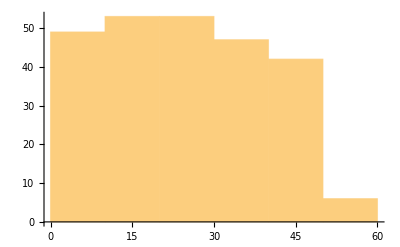

```mathematica
Histogram[%98]
```

```mathematica
Transpose[Join[{%98},{%96}]]
```

{{11,12},{16,25},{30,39},{33,12},{32,11},{4,7},{28,1},{25,31},{24,40},{39,3},{47,17},{36,20},{33,33},{35,41},{3,2},{14,1},{4,17},{24,25},{42,37},{3,18},{28,22},{17,2},{38,8},{50,41},{30,24},{15,2},{1,41},{6,40},{1,36},{45,30},{36,31},{40,35},{46,27},{7,21},{4,23},{4,43},{36,44},{24,31},{16,50},{13,12},{28,49},{14,49},{7,26},{17,35},{4,34},{38,50},{50,38},{33,17},{21,39},{31,28},{38,28},{31,1},{31,41},{9,12},{41,27},{7,11},{13,1},{38,27},{3,34},{24,42},{7,27},{50,16},{21,10},{29,10},{17,36},{36,45},{24,39},{35,1},{30,41},{48,11},{14,37},{6,49},{18,48},{22,15},{29,44},{47,19},{3,47},{42,41},{30,25},{4,18},{25,15},{22,49},{4,23},{16,33},{15,35},{17,11},{45,33},{47,30},{21,29},{29,2},{6,11},{40,34},{17,10},{19,46},{40,44},{24,15},{1,31},{42,42},{33,44},{29,25},{29,14},{13,21},{11,48},{8,5},{18,47},{38,3},{14,7},{42,45},{48,3},{30,13},{8,23},{46,47},{3,39},{41,49},{26,24},{19,20},{49,35},{49,24},{30,8},{7,34},{6,32},{41,45},{24,7},{19,44},{15,4},{10,32},{41,2},{34,45},{10,10},{15,49},{46,29},{24,1},{49,20},{11,39},{27,16},{35,14},{43,41},{49,44},{24,29},{35,38},{40,38},{9,43},{23,50},{10,49},{22,49},{17,18},{8,30},{25,9},{17,10},{46,2},{38,20},{29,27},{4,16},{10,22},{1,2},{26,16},{27,49},{36,1},{31,33},{13,41},{50,49},{41,16},{39,45},{13,22},{21,45},{20,11},{6,17},{43,1},{6,24},{18,25},{22,4},{25,3},{15,44},{49,11},{30,32},{23,48},{12,27},{4,39},{23,21},{27,12},{6,35},{40,41},{31,12},{7,26},{44,42},{30,10},{16,47},{26,42},{32,15},{27,24},{11,40},{22,14},{9,6},{7,39},{10,41},{6,31},{40,11},{24,8},{4,20},{2,1},{15,4},{36,12},{27,16},{50,20},{13,45},{12,15},{9,48},{47,11},{25,41},{22,45},{32,17},{19,40},{44,41},{1,36},{50,32},{38,5},{28,28},{48,38},{12,9},{43,30},{17,32},{29,29},{40,29},{9,40},{34,41},{24,26},{13,15},{43,41},{36,13},{14,35},{26,33},{4,30},{47,23},{38,12},{36,3},{6,14},{17,2},{12,16},{9,33},{22,40},{1,3},{25,16},{17,28},{11,6},{36,5},{23,7},{38,20},{4,27},{43,2},{35,9}}

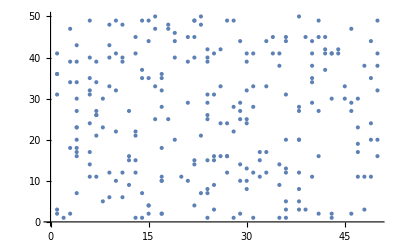

```mathematica
ListPlot[%101]
```

```mathematica
Table[RandomInteger[{1,50}],250]
```

{12,25,39,12,11,7,1,31,40,3,17,20,33,41,2,1,17,25,37,18,22,2,8,41,24,2,41,40,36,30,31,35,27,21,23,43,44,31,50,12,49,49,26,35,34,50,38,17,39,28,28,1,41,12,27,11,1,27,34,42,27,16,10,10,36,45,39,1,41,11,37,49,48,15,44,19,47,41,25,18,15,49,23,33,35,11,33,30,29,2,11,34,10,46,44,15,31,42,44,25,14,21,48,5,47,3,7,45,3,13,23,47,39,49,24,20,35,24,8,34,32,45,7,44,4,32,2,45,10,49,29,1,20,39,16,14,41,44,29,38,38,43,50,49,49,18,30,9,10,2,20,27,16,22,2,16,49,1,33,41,49,16,45,22,45,11,17,1,24,25,4,3,44,11,32,48,27,39,21,12,35,41,12,26,42,10,47,42,15,24,40,14,6,39,41,31,11,8,20,1,4,12,16,20,45,15,48,11,41,45,17,40,41,36,32,5,28,38,9,30,32,29,29,40,41,26,15,41,13,35,33,30,23,12,3,14,2,16,33,40,3,16,28,6,5,7,20,27,2,9}

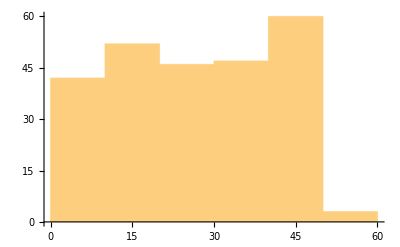

```mathematica
Histogram[%96]
```

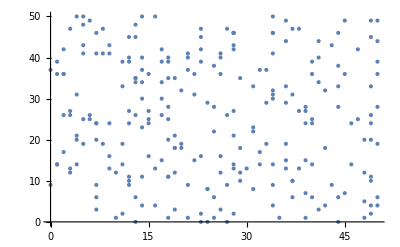

```mathematica
ListPlot[%91]
```

```mathematica
RandomInteger[{1,50}]
```

22

```mathematica
{im[ω,44,45,q,ϵ1,m],im[ω,26,32,q,ϵ1,m],im[ω,48,50,q,ϵ1,m],im[ω,μ,λ,q,0,m],im[ω,9,λ,q,ϵ1,m],im[ω,41,λ,q,ϵ1,m],im[ω,48,λ,q,ϵ1,m],im[ω,16,24,50,ϵ1,m],im[ω,7,25,48,ϵ1,m],im[ω,13,14,30,ϵ1,m],im[ω,25,35,45,ϵ1,m],im[ω,μ,λ,q,0,m],im[ω,26,λ,q,ϵ1,m],im[ω,10,21,39,ϵ1,m],im[ω,5,49,q,ϵ1,m],im[ω,μ,λ,q,0,m],im5[ω,10,28,31,46,47,ϵ1,m],im[ω,μ,45,q,ϵ1,m],im[ω,μ,λ,q,0,m],im[ω,23,λ,q,ϵ1,m],im[ω,μ,λ,q,0,m],im[ω,15,36,q,ϵ1,m],im[ω,μ,47,q,ϵ1,m],im5[ω,21,18,35,43,46,ϵ1,m],im[ω,6,λ,q,ϵ1,m],im5[ω,8,23,28,40,44,ϵ1,m],im[ω,13,24,q,ϵ1,m],im[ω,9,40,q,ϵ1,m],im[ω,35,λ,q,ϵ1,m],im[ω,0,34,0,ϵ1,m],im[ω,1,34,45,46,q,ϵ1,m],im[ω,10,47,q,ϵ1,m],im[ω,1,0,0,ϵ1,m],im4[ω,12,24,38,48,ϵ1,m],im[ω,19,21,q,ϵ1,m],im[ω,μ,50,q,ϵ1,m],im4[ω,5,19,39,45,ϵ1,m],im4[ω,8,22,23,31,ϵ1,m],im[ω,37,45,q,ϵ1,m],im5[ω,6,9,30,37,50,ϵ1,m],im[ω,4,49,q,ϵ1,m],im[ω,μ,λ,q,0,m],im[ω,27,λ,q,ϵ1,m],im[ω,34,λ,q,ϵ1,m],im[ω,29,39,q,ϵ1,m],im[ω,μ,λ,q,0,m],im[ω,8,25,q,ϵ1,m],im[ω,μ,λ,q,0,m],im[ω,9,10,33,ϵ1,m],im4[ω,8,27,41,45,ϵ1,m]}
```